```mathematica
f[x_]=Sin[x];
```

```mathematica
g[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
h[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1/2)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
i[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1/4)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
j[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1/6)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
k[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1/8)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
l[x_]=Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=1/10)^20 (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)];
```

```mathematica
p1=Plot[f[x],{x,0,12},PlotStyle->Purple];
```

```mathematica
p2=Plot[g[x],{x,0,12},PlotStyle->Blue];
```

```mathematica
p3=Plot[h[x],{x,0,12},PlotStyle->Green];
```

```mathematica
p4=Plot[i[x],{x,0,12},PlotStyle->Yellow];
```

```mathematica
p5=Plot[j[x],{x,0,12},PlotStyle->Orange];
```

```mathematica
p6=Plot[k[x],{x,0,12},PlotStyle->Pink];
```

```mathematica
p7=Plot[l[x],{x,0,12},PlotStyle->Red];
```

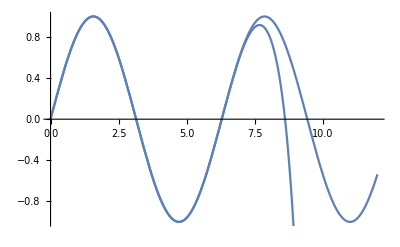

```mathematica
Show[p1,p2]
```

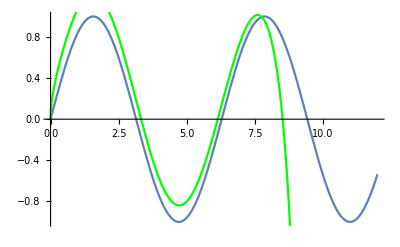

```mathematica
Show[p1,p3]
```

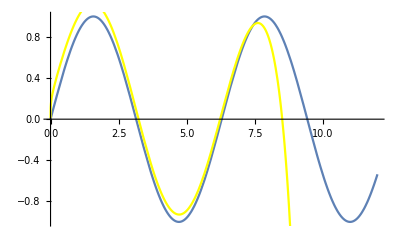

```mathematica
Show[p1,p4]
```

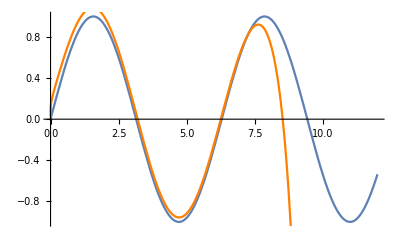

```mathematica
Show[p1,p5]
```

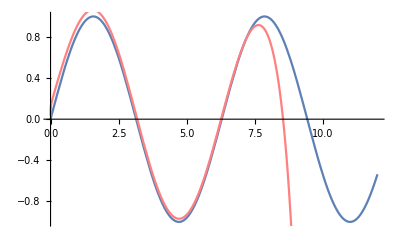

```mathematica
Show[p1,p6]
```

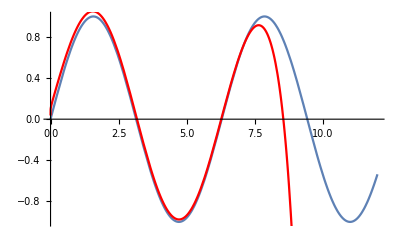

```mathematica
Show[p1,p7]
```

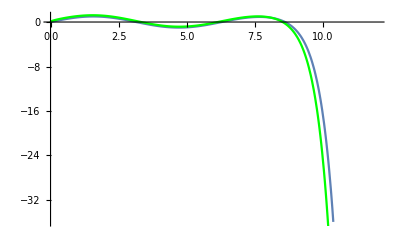

```mathematica
Show[p2,p3]
```

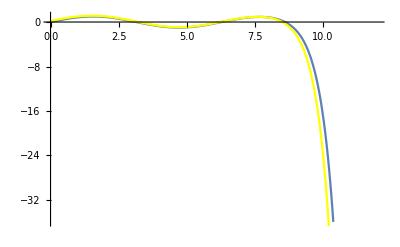

```mathematica
Show[p2,p4]
```

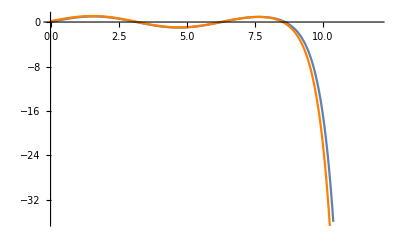

```mathematica
Show[p2,p5]
```

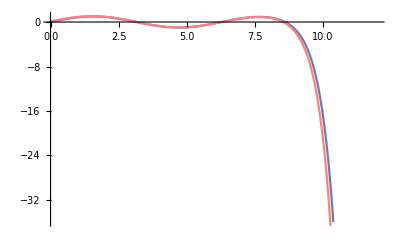

```mathematica
Show[p2,p6]
```

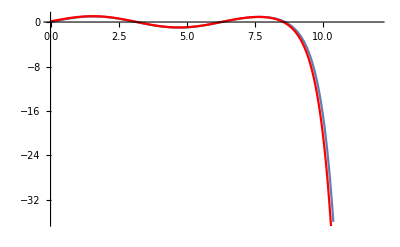

```mathematica
Show[p2,p7]
```

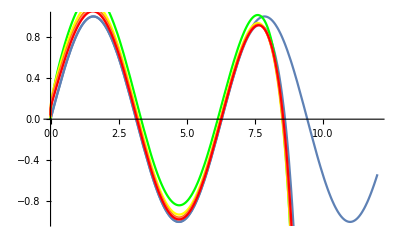

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7]
```

```mathematica
Manipulate[Expand[(D[Sin[x],{x,0}]/.{x->0})+∑_(k=p)^n (1/Gamma[k]*∫_0^x (Sin[x+(Pi k)/2 ]/.{x->0})*(x-t)^(k-1)ⅆt)],{n,0,10,p},{p,1/10,1,1/10}]
```